# Práctica 2.2

Alumno: Adrián Martínez Martínez

## Actividad 1

```mathematica
AFDtoAC[AFD_]:=Module[{Q,Σ,δ,S,F,i, f,j, aux},
Q=AFD[[1]];
Σ=AFD[[2]];
δ=AFD[[3]];
F=AFD[[5]];
S=Union[Q,Σ];
f={};

(* Si no es unidireccional, devuelve False *)
If[Length[δ[[1]]]!=3, Return[False]];

For[i=1,i<=Length[S],i++,
For[j=1,j<=Length[S],j++,
aux = Cases[δ, {S[[i]],S[[j]],_}];
If[Length[aux] > 0,
(*Then*)
AppendTo[f,aux[[1]]],
(*Else*)
(*Si ambos elementos son un símbolo del alfabeto o ambos son un estado, se deja el elemento de la célula*)
If[(MemberQ[Σ,S[[i]]] && MemberQ[Σ,S[[j]]]) || MemberQ[Q,S[[i]]] && MemberQ[Q,S[[j]]],
AppendTo[f,{S[[i]],S[[j]],S[[j]]}];
];
]
];
];

Return[{S,f,F}];
];
```

```mathematica
AFD = {{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},q,{r}};
ACB={{a,b,p,q,r},{{q,a,a,p},{q,a,b,p},{q,a,p,p},{q,a,q,p},{q,a,r,p},{q,b,a,r},{q,b,b,r},{q,b,p,r},{q,b,q,r},{q,b,r,r},{p,a,a,r},{p,a,b,r},{p,a,p,r},{p,a,q,r},{p,a,r,r},{p,b,a,q},{p,b,b,q},{p,b,p,q},{p,b,q,q},{p,b,r,q},{r,a,a,r},{r,a,b,r},{r,a,p,r},{r,a,q,r},{r,a,r,r},{r,b,a,r},{r,b,b,r},{r,b,p,r},{r,b,q,r},{r,b,r,r},{q,q,a,q},{q,q,b,q},{q,q,p,q},{q,q,q,q},{q,q,r,q},{q,p,a,p},{q,p,b,p},{q,p,p,p},{q,p,q,p},{q,p,r,p},{q,r,a,r},{q,r,b,r},{q,r,p,r},{q,r,q,r},{q,r,r,r},{p,q,a,q},{p,q,b,q},{p,q,p,q},{p,q,q,q},{p,q,r,q},{p,p,a,p},{p,p,b,p},{p,p,p,p},{p,p,q,p},{p,p,r,p},{p,r,a,r},{p,r,b,r},{p,r,p,r},{p,r,q,r},{p,r,r,r},{r,q,a,q},{r,q,b,q},{r,q,p,q},{r,q,q,q},{r,q,r,q},{r,p,a,p},{r,p,b,p},{r,p,p,p},{r,p,q,p},{r,p,r,p},{r,r,a,r},{r,r,b,r},{r,r,p,r},{r,r,q,r},{r,r,r,r},{a,a,a,a},{a,a,b,a},{a,a,p,a},{a,a,q,a},{a,a,r,a},{a,b,a,b},{a,b,b,b},{a,b,p,b},{a,b,q,b},{a,b,r,b},{b,a,a,a},{b,a,b,a},{b,a,p,a},{b,a,q,a},{b,a,r,a},{b,b,a,b},{b,b,b,b},{b,b,p,b},{b,b,q,b},{b,b,r,b}},{r}};
AC = AFDtoAC[AFD];
AC
```

{{a,b,p,q,r},{{a,a,a},{a,b,b},{b,a,a},{b,b,b},{p,a,r},{p,b,q},{p,p,p},{p,q,q},{p,r,r},{q,a,p},{q,b,r},{q,p,p},{q,q,q},{q,r,r},{r,a,r},{r,b,r},{r,p,p},{r,q,q},{r,r,r}},{r}}

## Actividad 2

Esta segunda actividad se trata de implementar un módulo que, tomando como entrada una cadena arbitraria, un AC que reconoce un lenguaje mediante entrada paralela en tiempo real y un estado frontera q ∈ S, proporcione como salida True si el AC acepta la cadena y False en caso contrario.

```mathematica
Actividad2[AC_List, word_List, q_]:=Module[{f, isBidirectional,w1,w2, i,reps, state},
f=AC[[2]];
w1=word;
w2=word;
isBidirectional = Length[f[[1]]]==4;

If[isBidirectional,
For[reps=1,reps<=Length[word],reps++,
For[i=1,i<=Length[word],i++,
If [i==1,
state=Cases[f,{q,w1[[i]],w1[[i+1]],_}]
,
If [i== Length[word],
state=Cases[f,{w1[[i-1]],w1[[i]],q,_}],
(*Else*)
state=Cases[f,{w1[[i-1]],w1[[i]],w1[[i+1]],_}];
]];
w2[[i]] = state[[1,4]]
];
w1=w2;
];
];

If[!isBidirectional,
For[reps=1,reps<=Length[word],reps++,
For[i=1,i<=Length[word],i++,
If [i==1,
state=Cases[f,{q,w1[[i]],_}],
(*Else*)
state=Cases[f,{w1[[i-1]],w1[[i]],_}];
];
w2[[i]] = state[[1,3]]
];
w1=w2;
];
];

Return[MemberQ[ AC[[3]], w1[[Length[word]]]]];
];
```

```mathematica
w={a,b,a,a,b};
Actividad2[AC, w,q]
```

True

```mathematica
(*Prueba para Automata Celular Bidireccional *)
Actividad2[ACB, w,q]
```

True

### Actividad 3

Para la última actividad de esta práctica de pide implementar un módulo que muestre la secuencia de computación que se lleva a cabo en el módulo propuesto en la actividad 2 mediante un diagrama espacio temporal. Para este ejercicio se parte del módulo anterior pero se plotea las diferentes iteraciones. Además se hace uso de un CharacterArrayPlot para mostrar la leyenda de color de los díferentes símbolos de S del autómata celular:

```mathematica
Actividad3[AC_List, word_List, q_]:=Module[{S,f, isBidirectional,w1,w2, i,reps, state, colors, colorRules, colorLegend, charRules,
								sol, aux,frame, solColorRules},
S=AC[[1]];
f=AC[[2]];
w1=word;
w2=word;
isBidirectional = Length[f[[1]]]==4;
colors = RandomColor[Length[S]];
colorRules = {};
colorLegend = {};
charRules = {};
solColorRules={};
sol={};
aux={};
AppendTo[aux, word];

For[i=1,i<=Length[S], i++,
	AppendTo[colorRules, i->colors[[i]]];
	AppendTo[solColorRules, S[[i]]->colors[[i]]];
	AppendTo[colorLegend, i];
	AppendTo[charRules, i->S[[i]]];
];

frame=ArrayPlot[aux, ColorRules->solColorRules, Mesh->All, MeshStyle->Black];
AppendTo[sol, frame];

Print[
ResourceFunction["CharacterArrayPlot"][{colorLegend},
ColorRules->colorRules,
"CharacterRules"-> charRules]
];

If[isBidirectional,
For[reps=1,reps<=Length[word],reps++,
For[i=1,i<=Length[word],i++,
If [i==1,
state=Cases[f,{q,w1[[i]],w1[[i+1]],_}]
,
If [i== Length[word],
state=Cases[f,{w1[[i-1]],w1[[i]],q,_}],
(*Else*)
state=Cases[f,{w1[[i-1]],w1[[i]],w1[[i+1]],_}];
]];
w2[[i]] = state[[1,4]]
];
PrependTo[aux, w2];
frame=ArrayPlot[aux, ColorRules->solColorRules, Mesh->All, MeshStyle->Black];
AppendTo[sol, frame];
w1=w2;
w1=w2;
];
];

If[!isBidirectional,
For[reps=1,reps<=Length[word],reps++,
For[i=1,i<=Length[word],i++,
If [i==1,
state=Cases[f,{q,w1[[i]],_}],
(*Else*)
state=Cases[f,{w1[[i-1]],w1[[i]],_}];
];
w2[[i]] = state[[1,3]]
];
PrependTo[aux, w2];
frame=ArrayPlot[aux, ColorRules->solColorRules, Mesh->All, MeshStyle->Black];
AppendTo[sol, frame];
w1=w2;
];
];
Return[ListAnimate[sol]];
];
```

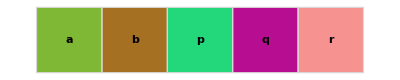

```mathematica
w={a,b,a,a,b};
Actividad3[AC, w,q]
```

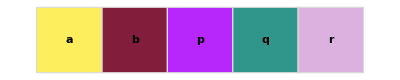

```mathematica
(*Prueba para Automata Celular Bidireccional *)
Actividad3[ACB, w,q]
```